Ejercicio  5 
Dada la función de distribución 
F(x)=Piecewise[{{0, x<-1}, {(x+1)/9, -1≤x<0}, {(x^2+2)/9, 0≤x<2}, {1, x≥2}}]
      a⟩Descomponer F como mixtura de funciones de distribución. 
Dar las funciones de probabilidad y de densidad correspondientes y representar todas las funciones.
b⟩ Calcular  P_X[[-1/2,3)], P_X[(-1,0)∪(1,2)], P_X[2X^2+|X|>1]

```mathematica
F[x_] := Piecewise[{{0, x<-1}, {(x+1)/9, -1<=x<0}, {(x^2+2)/9, 0<=x<2}, {1, x>=2}}]
```

```mathematica
F[x]
```

Piecewise[{{0, x<-1}, {(1+x)/9, -1≤x<0}, {1/9 (2+x^2), 0≤x<2}, {1, x≥2}, {0, True}}]

```mathematica
Simplify[%] (*No sirve de nada simplificar xd*)
```

Piecewise[{{1, x≥2}, {(1+x)/9, -1≤x<0}, {1/9 (2+x^2), 0≤x<2}, {0, True}}]

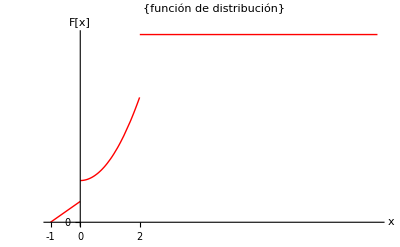

```mathematica
Plot[ F[x] ,{x,-1, 10}, PlotRange->{{-1,10},{0,1}}, AxesLabel->{"x","F[x]"}, PlotStyle->{Red,Thick},  PlotLabel->{"función de distribución"}, Ticks->{{-1, 0,2}}]
```

```mathematica
F[2]
```

1

```mathematica
Limit[F[t],t->2, Direction->1]//N
```

0.666667

```mathematica
F[0]
```

2/9

```mathematica
Limit[F[t],t->0, Direction->1]//N
```

0.111111

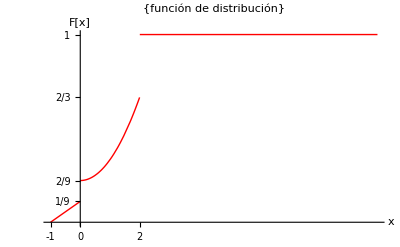

```mathematica
Plot[ F[x] ,{x,-1, 10}, PlotRange->{{-1,10},{0,1}}, AxesLabel->{"x","F[x]"}, PlotStyle->{Red,Thick},  PlotLabel->{"función de distribución"}, Ticks->{{-1, 0,2}, {1/9, 2/9, 2/3, 1}}]
```

```mathematica
Fd[x_]:=Piecewise[{{0,x<0},{1/9,0≤x<2},{4/9,x>=2}}]
```

```mathematica
Fd[x]
```

Piecewise[{{0, x<0}, {1/9, 0≤x<2}, {4/9, x≥2}, {0, True}}]

□

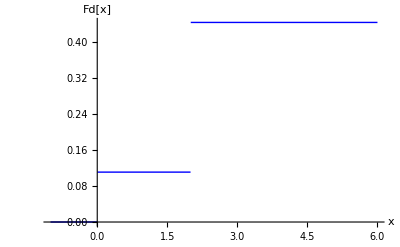

```mathematica
Plot[Fd[x],{x,-1,6}, AxesLabel->{"x","Fd[x]"},PlotStyle->{{Blue,Thick}} ]
```

```mathematica
Fc[x_]:=F[x]-Fd[x]
```

```mathematica
Fc[x]
```

-(Piecewise[{{0, x<0}, {1/9, 0≤x<2}, {4/9, x≥2}, {0, True}}])+(Piecewise[{{0, x<-1}, {(1+x)/9, -1≤x<0}, {1/9 (2+x^2), 0≤x<2}, {1, x≥2}, {0, True}}])

```mathematica
Simplify[%]
```

Piecewise[{{5/9, x≥2}, {(1+x)/9, -1≤x<0}, {1/9 (1+x^2), 0≤x<2}, {0, True}}]

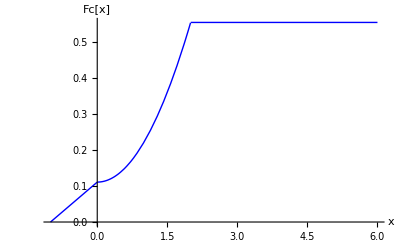

```mathematica
Plot[Fc[x],{x,-1,6}, AxesLabel->{"x","Fc[x]"},PlotStyle->{{Blue,Thick}} ]
```

```mathematica
Limit[Fd[x],x->∞]
```

4/9

```mathematica
F1[x_]:=Fd[x]/(4/9)
```

```mathematica
F1[x]
```

9/4 (Piecewise[{{0, x<0}, {1/9, 0≤x<2}, {4/9, x≥2}, {0, True}}])

```mathematica
Simplify[%]
```

Piecewise[{{1/4, 0≤x<2}, {1, x≥2}, {0, True}}]

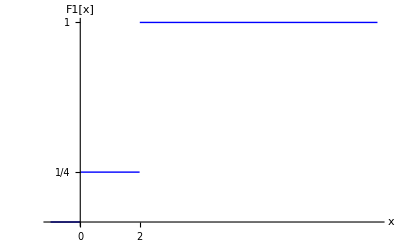

```mathematica
Plot[F1[x],{x,-1,10}, AxesLabel->{"x","F1[x]"},PlotStyle->{{Blue,Thick}}, Ticks->{{0,2},{1/4,1}} ]
```

```mathematica
F2[x_]:=Fc[x]/(5/9)
```

```mathematica
F2[x]
```

9/5 (-(Piecewise[{{0, x<0}, {1/9, 0≤x<2}, {4/9, x≥2}, {0, True}}])+(Piecewise[{{0, x<-1}, {(1+x)/9, -1≤x<0}, {1/9 (2+x^2), 0≤x<2}, {1, x≥2}, {0, True}}]))

```mathematica
Simplify[F2[x]]
```

Piecewise[{{1, x≥2}, {(1+x)/5, -1≤x<0}, {1/5 (1+x^2), 0≤x<2}, {0, True}}]

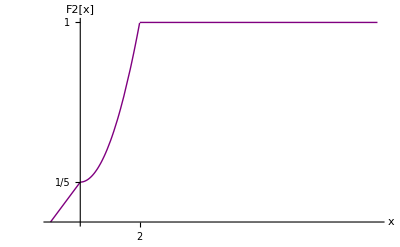

```mathematica
Plot[F2[x],{x,-1,10}, PlotRange->All, AxesLabel->{"x","F2[x]"},PlotStyle->{{Purple,Thick}}, Ticks->  {{2},{1/5,1}}]
```

```mathematica
f[x_]=D[F[x],x]
```

Piecewise[{{0, x<-1}, {1/9, -1<x<0}, {(2 x)/9, 0<x<2}, {0, x>2}, {Indeterminate, True}}]

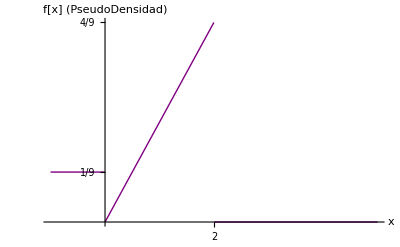

```mathematica
Plot[f[x],{x,-1,5}, PlotRange->All, AxesLabel->{"x","f[x] (PseudoDensidad)"},PlotStyle->{{Purple,Thick}}, Ticks->  {{2},{1/9,4/9}}]
```

```mathematica
P[x_]:=F[x]-Limit[F[t], t->x, Direction->1]
```

```mathematica
a = Limit[Fd[x],x->∞]
```

4/9

```mathematica
P[0]+P[2]+Integrate[f[x], {x,-∞,∞}] (*Comrpobamos que *)
```

1

```mathematica
P[0]
```

1/9

F[x] = a F1[x] + (1-a)F2[x] 
P_X[[-1/2,3)], P_X[(-1,0)∪(1,2)], P_X[2X^2+|X|>1]

```mathematica
Px[x_,y_]=Limit[F[t], t->y, Direction->1] - Limit[F[t], t->x, Direction->1]
```

-(Piecewise[{{1, x>2}, {(1+x)/9, -1<x≤0}, {1/9 (2+x^2), 0<x≤2}, {0, True}}])+(Piecewise[{{1, y>2}, {(1+y)/9, -1<y≤0}, {1/9 (2+y^2), 0<y≤2}, {0, True}}])

```mathematica
a = Px[-1/2, 3] (*Px([-1/2, 3])*)
```

17/18

```mathematica
b = Px[-1, 0]+Px[1,2] (*Px((-1, 0) U (1, 2))*)
```

4/9

```mathematica
c=Px[-∞,-0.5]+Px[0.5,∞] (*Px(2x^2 + |x| > 1)*)
```

0.805556